```mathematica
foo:=Table[Integrate[Cos[π/2*x^2],{x,0,α}],{α,0,10,.01}]
bar:=Table[
{Integrate[Cos[π/2*x^2],{x,0,α}],Integrate[Sin[π/2*x^2],{x,0,α}]},
{α,0,10,.01}
]
negBar:=Table[
{-1*Integrate[Cos[π/2*x^2],{x,0,α}],-1*Integrate[Sin[π/2*x^2],{x,0,α}]},
{α,0,10,.01}
]
```

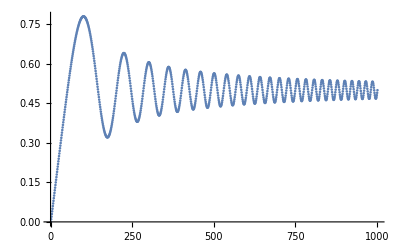

```mathematica
ListPlot@foo
(*does not look like the Cornu Spiral, but the integral looks like it converges to .5 for a really large upper-bound on its integration.

todo: draw the Cornu Spiral
attempt: compute the values of each fresnel integral, for some range.
Then, plot one against the other.

Success.
Note, the negative portion of the spiral is contained within another list; they are both plotted simultaneously - see below.

*)
```

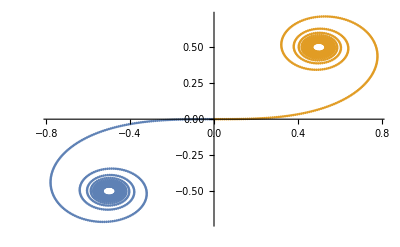

```mathematica
ListPlot[{negBar,bar}]
```

```mathematica
del:=Table[Integrate[Cos[π/2*x^2],{x,0,α}],{α,0,5,.01}]
ta:=Table[Integrate[Sin[π/2*x^2],{x,0,α}],{α,0,5,.01}]
```

```mathematica
cornuSpiral:={}
For[i=1,i<Length@del+1,i++,
AppendTo[cornuSpiral,{del[[i]],ta[[i]]}]
]
```

```mathematica
cornuSpiralTable:=Table[{del[[i]],ta[[i]]},{i,1,Length@del+1}]
```

```mathematica
ListPlot[cornuSpiralTable]
```

1001

```mathematica
cornuSpiralTable
```